```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phase data_v3

```mathematica
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,900,1200,10}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,900,1200,10}];
r42=chi4/chi2;
```

```mathematica
(*r42[[1;;45]][[1;;60]]=1;
r42[[46;;55]][[1;;50]]=1;
r42[[56;;62]][[1;;40]]=1;
r42[[63;;78]][[1;;20]]=1;
r42[[79;;84]][[1;;15]]=1;
r42[[85;;88]][[1;;10]]=1;*)
```

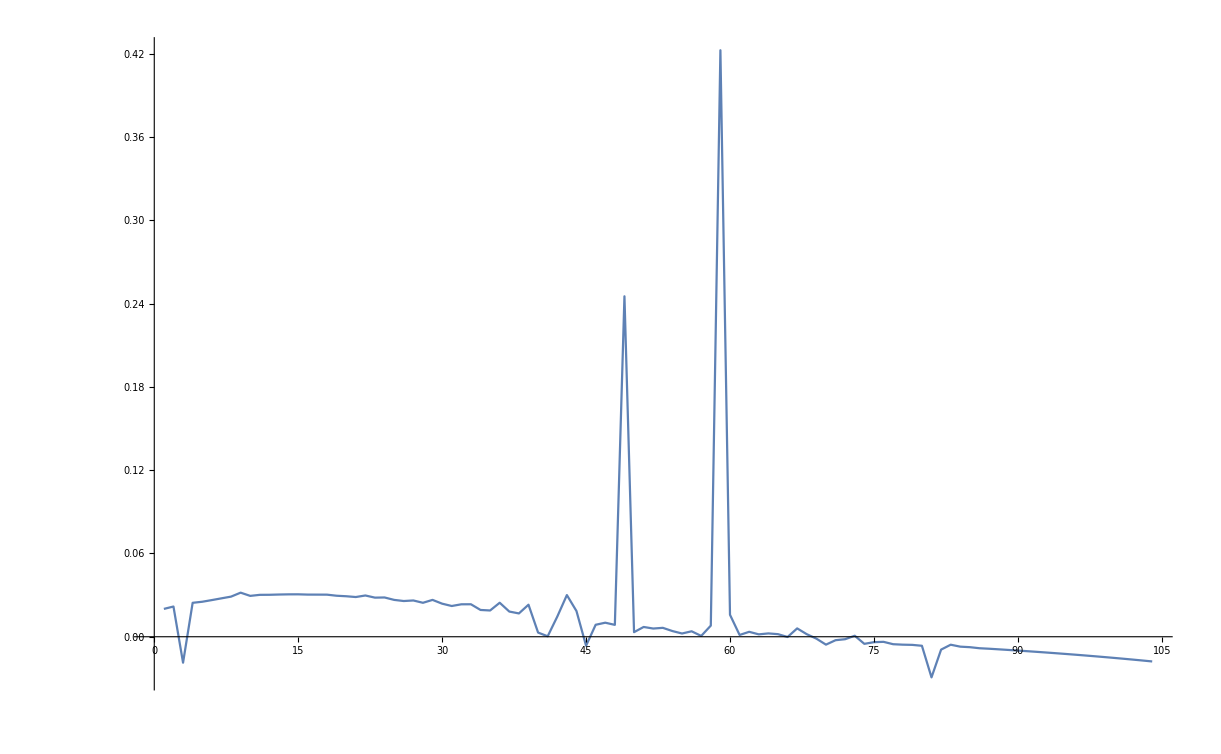

```mathematica
ListLinePlot[r42[[9]],PlotRange->{All,All}]
```

```mathematica
ListDensityPlot[Transpose[r42],PlotRange->{All,All,{-5,5}}]
```

-Graphics-